```mathematica
(*Author: Jakob Zimmermann*)
(*Code available at: https://github.com/zimmermannJakob/InfectionSpreadingOnNetworks*)
```

```mathematica
(*Setting random seed for reproductivity of results*)
SeedRandom[42]; 
(*Setting the number of Nodes (People in the Simulation)*)
numNodes = 1000;
(*statusList keeps track of the status of each node ;
0: S;
1: I;
2: R
*) 
statusList = ConstantArray[0,numNodes]; 
(*infectionTimeList keeps track of the time each node has been infected (initilized with '-1')*)
infectionTimeList = ConstantArray[-1,numNodes];

(*Defining the number of infected people at t=0*)
startInfectionNumber = 3;
(*Defining the number of itteration steps it takes for a person to get from I->R*)
transitionIR = 5;
(*Probability with which an infected node infects another adjacent node, which is in S*)
infectionRate = .4;
(*Maximum itteration steps*)
tMax = 30;
(*defining tCurrent to keep track of the number of itterations which are actually needed*)
tCurrent = 0;

(*Defining the Graph (how nodes are connected)*)
graph = RandomGraph[BarabasiAlbertGraphDistribution[numNodes,2]];
(*number of people in S, I and R respectively*)
numS = numNodes - startInfectionNumber;
numI = startInfectionNumber;
numR = 0;
(*Initializing S(t), I(t), R(t)*)
listS = List[];
listI = List[];
listR = List[];
(*Initializing statusList(t) and infectionTimeList(t)*)
infectionTimeListT = List[];
statusListT = List[];
(*Infecting startInfectionNumber-people, picked random out of all nodes*)
firstInfectionList = Table[RandomInteger[{1,numNodes}],startInfectionNumber];
(*Updating statusList and infectionTimeList to infect the random selected nodes from before*)
For[i = 0, i<Length[firstInfectionList]  ,i++;
statusList[[firstInfectionList[[i]]]] = 1;
infectionTimeList[[firstInfectionList[[i]]]] = transitionIR-1;
]
(*Updating numS(t), numI(t) and numR(t)*)
AppendTo[listS,numS];
AppendTo[listI,numI];
AppendTo[listR,numR];
(*Updating infectionTimeList(t) and statusList(t)*)
AppendTo[infectionTimeListT,infectionTimeList];
AppendTo[statusListT,statusList];

(*Start of the actual simulation here*)
For[t = 0, t<tMax && numI !=0,t++;
tCurrent++;

(*infecting people*)
infectedNodes = List[];
(*save every node to a seperate list*)
For[nodeIndex = 0, nodeIndex< numNodes,nodeIndex++;
If[statusList[[nodeIndex]] == 1,
AppendTo[infectedNodes, nodeIndex];
];
];
(*for every infected node: infect neighbors:*)
For[infectedNodesIndex = 0, infectedNodesIndex< Length[infectedNodes],infectedNodesIndex++;
(*get neighbors*)
adjList = AdjacencyList[graph, infectedNodes[[infectedNodesIndex]]];
For[neighborIndex = 0, neighborIndex<Length[adjList], neighborIndex++;
(*If the node is not infected yet, infect it with the probability of infection rate*)
If[RandomReal[]<=infectionRate && statusList[[adjList[[neighborIndex]]]]==0,
statusList[[adjList[[neighborIndex]]]] = 1;
infectionTimeList[[adjList[[neighborIndex]]]] = transitionIR;
(*update the number of susceptable and infected people*)
numS--;
numI++;
];

];
];

(*removing people*)
(*for every node ...*)
For[nodeIndex = 0, nodeIndex< numNodes, nodeIndex++;
(*... if the node is infected...*)
If[infectionTimeList[[nodeIndex]] !=-1,
(**... reduce the days the node is infected by 1*)
infectionTimeList[[nodeIndex]] = infectionTimeList[[nodeIndex]] -1;
(*If the status goes back to not being infected...*)
If[infectionTimeList[[nodeIndex]] ==-1,
(*update the status*)
statusList[[nodeIndex]] = 2;
(*update the number of infected and removed people*)
numI--;
numR++;
];

];
];

(*Appending after each itteration*)
AppendTo[listS,numS];
AppendTo[listI,numI];
AppendTo[listR,numR];
(*Updating infectionTimeList(t) and statusList(t)*)
AppendTo[infectionTimeListT,infectionTimeList];
AppendTo[statusListT,statusList];
]
```

```mathematica
Plot the course of the epidemic
```

course epidemic of Plot the^2

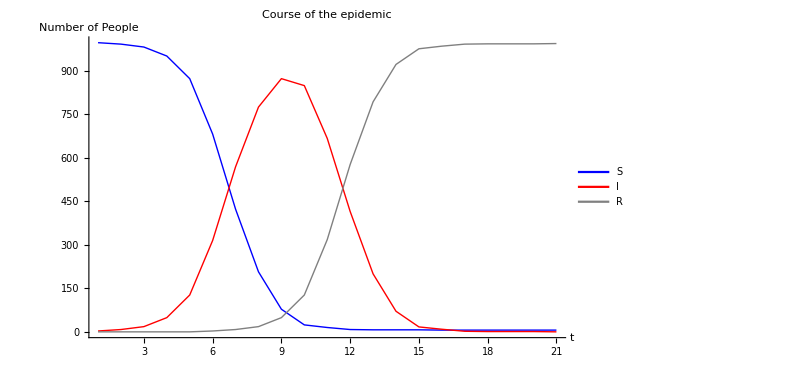

```mathematica
(*Plotting course of the compartment S*)
plotS = ListLinePlot[listS, PlotStyle->{Blue, Thick}, 
AxesLabel->{"t","Number of People"}, 
PlotLegends->{"S"}];
(*Plotting course of the compartment I*)
plotI = ListLinePlot[listI,PlotStyle-> {Red, Thick}, PlotLegends->{"I"}];
(*Plotting course of the compartment R*)
plotR = ListLinePlot[listR, PlotStyle-> {Gray, Thick}, PlotLegends->{"R"}];
(*Showing all the plots created above in one image*)
img = Show[plotS, plotI, plotR, PlotRange->All, 
PlotLabel -> "Course of the epidemic"]
```

```mathematica
Simulation-visualized
```

Simulation-visualized

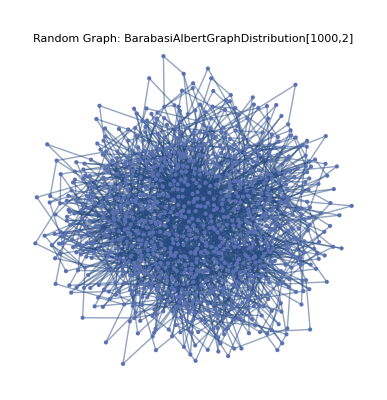

```mathematica
graphConnectivity = VertexDegree[graph];
maxConnection = Max[graphConnectivity];

(*Changing the size of the nodes (doesn't work with large numbers of nodes)*)
For[i = 1, i<= Length[graphConnectivity], i++,
graph = Annotate[graph, VertexSize->{(i ->graphConnectivity[[i]]/(10))}]
]
(*Annotate the graph to have thin edges and labels*)
graph = Annotate[graph, {EdgeStyle->Thin, PlotLabel->"Random Graph:" BarabasiAlbertGraphDistribution[numNodes,2]}]
(*-------------------*)
(*creating the animation object*)
animation = Animate[HighlightGraph[graph,{Style[Flatten[Position[statusListT[[aniStep]],0]],Blue], Style[Flatten[Position[statusListT[[aniStep]],1]],Red], Style[Flatten[Position[statusListT[[aniStep]],2]],Gray]
} ],{aniStep,1,tCurrent+1,1},AnimationRunning->False, AnimationRate->2]
```

```mathematica
Comparision to SIR with differential equations
```

Comparision differential equations SIR to with

```mathematica
Clear[s,i,r,β,γ,n, t]

β = Mean[VertexDegree[graph]]; (*average number of contacts per node*)
γ = infectionRate;  
n = numNodes;
sol = NDSolve[{
s'[t] == -(β i[t] s[t])/n,
i'[t] == (β i[t] s[t])/n-γ i[t],
r'[t] == γ i[t],

s[0] == n - startInfectionNumber,
i[0] == startInfectionNumber,
r[0] == 0
},
{s,i,r},
{t,tCurrent}
];
```

```mathematica
Plotting of the result
```

of Plotting result the

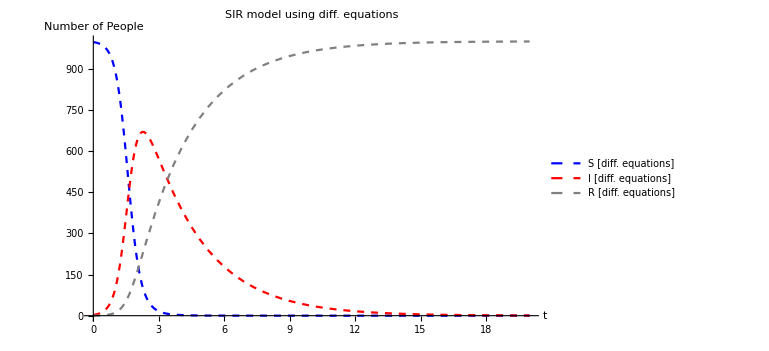

```mathematica
solutionS=First[s/.sol];
solutionI=First[i/.sol];
solutionR=First[r/.sol];

plotDiffEqu = Plot[{solutionS[t],solutionI[t],solutionR[t]},{t,0,tCurrent}, PlotStyle->{{Dashed, Blue}, {Dashed, Red}, {Dashed, Gray}}, PlotLabel->"SIR model using diff. equations", PlotLegends->{"S [diff. equations]","I [diff. equations]","R [diff. equations]"}, AxesLabel->{"t", "Number of People"}]
```

```mathematica
Direct comparison
```

comparison Direct

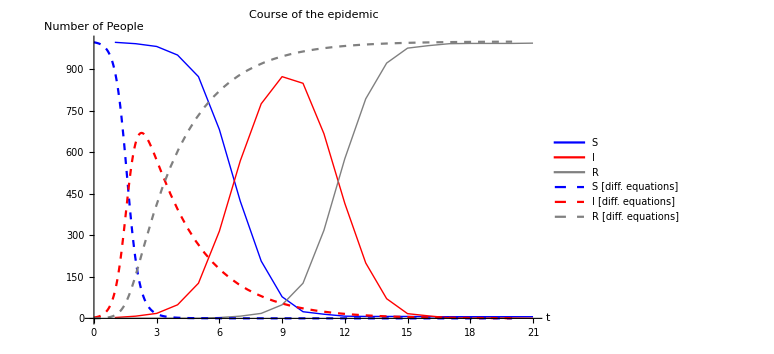

```mathematica
Show[img, plotDiffEqu]
```

```mathematica
Different Random-Graphs with different Vertex connectivities
```

Different Random-connectivities different Graphs Vertex with

```mathematica
(*Using the bernoulli-graph distribution (bernoulli distribution with E[X] = n*p )*)
(*Three models of connectivity: 
-very few superspreaders (e.g practicing of good social distancing, sparse settled regions);
  -a lot of superspreaders (e.g densly populated areas, frequent events with a lot of person to person contacts); 
*)
```

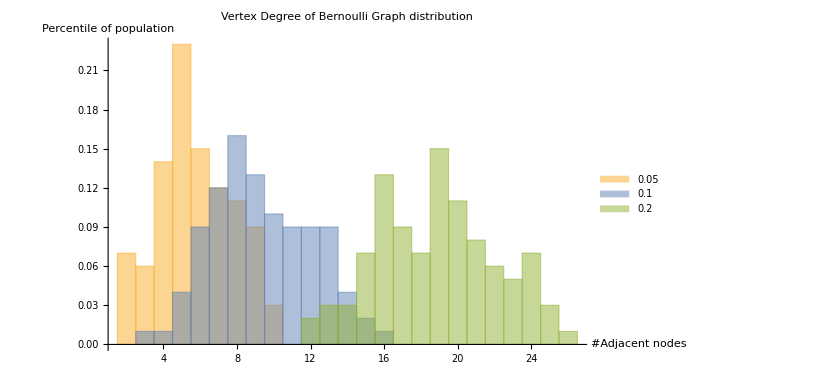

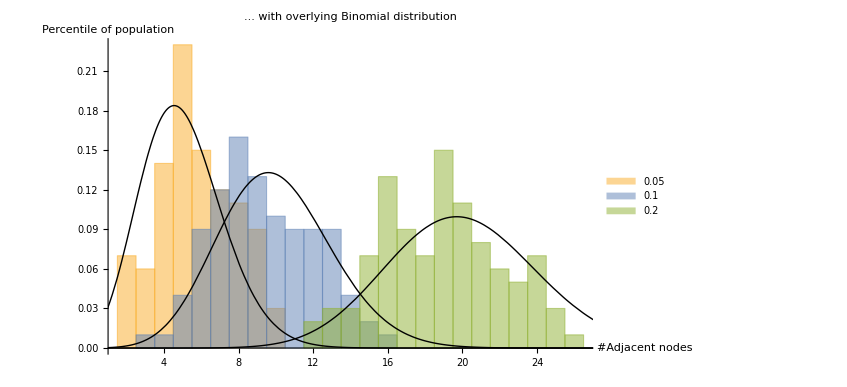

```mathematica
SeedRandom[42];
n = 100;
(*defining the probability used for crating the graphs in listP*)
listP = {N[5/n],N[10/n],N[20/n]};
(*listD is used to store the vertex degree for the three models used*)
listD = {};

(*Plot the PDF for every element of listP using the binomial distribution with p ∈ listP*)
pdfPlot = Plot[Evaluate@Table[PDF[BinomialDistribution[n,p],x],{p,listP}],{x,0,n},
PlotRange->All,
PlotStyle->{{Thick, Black},{Thick, Black},{Thick, Black}}
];

(*Get the vertex degree for every graph*)
For[i = 1, i<=Length[listP], i++,
g=RandomGraph[BernoulliGraphDistribution[n,listP[[i]]]];
AppendTo[listD, VertexDegree[g]];
]
(*plot the hists for every obtained vertex degree*)
pdfHist = Histogram[listD,n-1,"PDF", PlotRange->All, ChartLegends->listP, PlotLabel->"Vertex Degree of Bernoulli Graph distribution", AxesLabel->{"#Adjacent nodes", "Percentile of population"}]

(*showing the hists overlayed with the PDF of the Binomial distribution*)
Show[pdfHist, pdfPlot, PlotLabel->"... with overlying Binomial distribution"]
```

```mathematica
Running the simulation with different distributions
```

different distributions Running simulation the with

Sparse

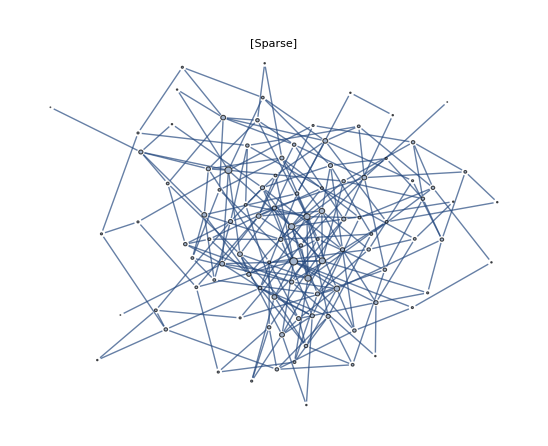

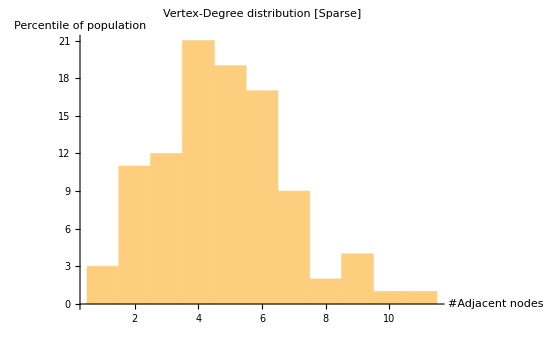

Balanced

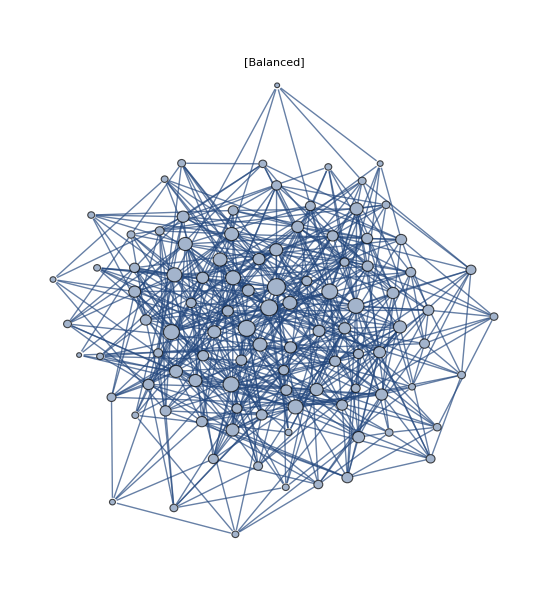

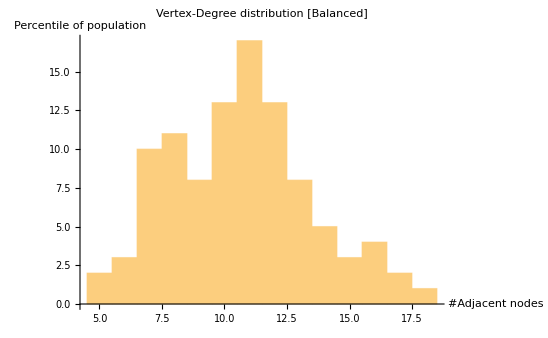

Dense

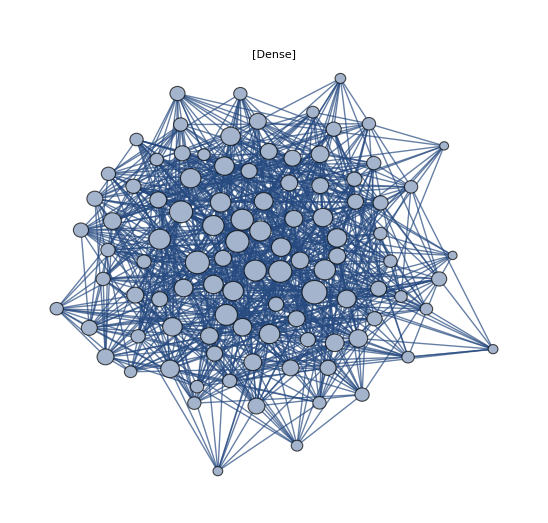

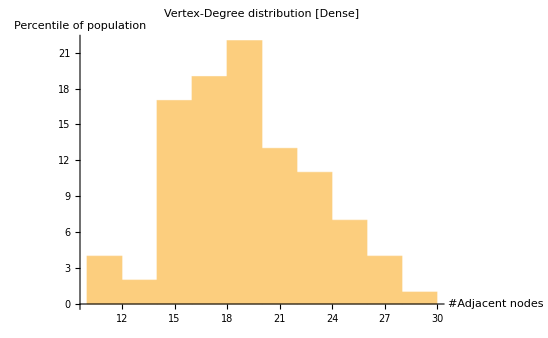

```mathematica
scaling = 20;
Sparse 
graphSparse = RandomGraph[BernoulliGraphDistribution[n ,listP[[1]]]];
(*Annotating the graph*)
graphConnectivity = VertexDegree[graphSparse];
maxConnection = Max[graphConnectivity];
For[i = 1, i<= Length[graphConnectivity], i++,
graphSparse = Annotate[graphSparse, VertexSize->{(i ->graphConnectivity[[i]]/(scaling))}]
]
graphSparse = Annotate[graphSparse, {EdgeStyle->Thin, PlotLabel->"[Sparse]"}]

(*plotting the histogram*)
Show[VertexDegree[graphSparse]//Histogram,PlotLabel->"Vertex-Degree distribution [Sparse]",AxesLabel->{"#Adjacent nodes", "Percentile of population"}]



Balanced
graphBalanced = RandomGraph[BernoulliGraphDistribution[n,listP[[2]]]];

(*Annotating the graph*)
graphConnectivity = VertexDegree[graphBalanced];
maxConnection = Max[graphConnectivity];
For[i = 1, i<= Length[graphConnectivity], i++,
(*every node gets a corresponding size depending of connectivity and scaling*)
graphBalanced = Annotate[graphBalanced, VertexSize->{(i ->graphConnectivity[[i]]/(scaling))}]
]
(*change the edges to be thin*)
graphBalanced = Annotate[graphBalanced, {EdgeStyle->Thin,PlotLabel->"[Balanced]"}]

(*plotting the histogram*)
Show[VertexDegree[graphBalanced] // Histogram, PlotLabel->"Vertex-Degree distribution [Balanced]", AxesLabel->{"#Adjacent nodes", "Percentile of population"}]



Dense
graphDense = RandomGraph[BernoulliGraphDistribution[n,listP[[3]]]];

(*Annotating the graph*)
graphConnectivity = VertexDegree[graphDense];
maxConnection = Max[graphConnectivity];
For[i = 1, i<= Length[graphConnectivity], i++,
graphDense = Annotate[graphDense, VertexSize->{(i ->graphConnectivity[[i]]/(scaling))}]
]
graphDense = Annotate[graphDense, {EdgeStyle->Thin, PlotLabel->"[Dense]"}]

(*Plotting the histogram*)
Show[VertexDegree[graphDense] // Histogram, PlotLabel->"Vertex-Degree distribution [Dense]", AxesLabel->{"#Adjacent nodes", "Percentile of population"}]
```

Defining the Algorithm as a function

```mathematica
epidemicSimulation[graph_,numNodes_, startInfectionNumber_,transitionIR_,infectionRate_,tMax_  ] := {(*Setting random seed for reproductivity of results*)
SeedRandom[42]; 
(*statusList keeps track of the status of each node ;
0: S;
1: I;
2: R
*) 
statusList = ConstantArray[0,numNodes]; 
(*infectionTimeList keeps track of the time each node has been infected (initilized with '-1')*)
infectionTimeList = ConstantArray[-1,numNodes];

(*defining tCurrent to keep track of the number of itterations which are actually needed*)
tCurrent = 0;

(*number of people in S, I and R respectively*)
numS = numNodes - startInfectionNumber;
numI = startInfectionNumber;
numR = 0;
(*Initializing S(t), I(t), R(t)*)
listS = List[];
listI = List[];
listR = List[];
(*Initializing statusList(t) and infectionTimeList(t)*)
infectionTimeListT = List[];
statusListT = List[];
(*Infecting startInfectionNumber-people, picked random out of all nodes*)
firstInfectionList = Table[RandomInteger[{1,numNodes}],startInfectionNumber];
(*Updating statusList and infectionTimeList to infect the random selected nodes from before*)
For[i = 0, i<Length[firstInfectionList]  ,i++;
statusList[[firstInfectionList[[i]]]] = 1;
infectionTimeList[[firstInfectionList[[i]]]] = transitionIR-1;
]
(*Updating numS(t), numI(t) and numR(t)*)
AppendTo[listS,numS];
AppendTo[listI,numI];
AppendTo[listR,numR];
(*Updating infectionTimeList(t) and statusList(t)*)
AppendTo[infectionTimeListT,infectionTimeList];
AppendTo[statusListT,statusList];

(*Start of the actual simulation here*)
For[t = 0, t<tMax && numI !=0,t++;
tCurrent++;

(*infecting people*)
infectedNodes = List[];
(*save every node to a seperate list*)
For[nodeIndex = 0, nodeIndex< numNodes,nodeIndex++;
If[statusList[[nodeIndex]] == 1,
AppendTo[infectedNodes, nodeIndex];
];
];
(*for every infected node: infect neighbors:*)
For[infectedNodesIndex = 0, infectedNodesIndex< Length[infectedNodes],infectedNodesIndex++;
(*get neighbors*)
adjList = AdjacencyList[graph, infectedNodes[[infectedNodesIndex]]];
For[neighborIndex = 0, neighborIndex<Length[adjList], neighborIndex++;
(*If the node is not infected yet, infect it with the probability of infection rate*)
If[RandomReal[]<=infectionRate && statusList[[adjList[[neighborIndex]]]]==0,
statusList[[adjList[[neighborIndex]]]] = 1;
infectionTimeList[[adjList[[neighborIndex]]]] = transitionIR;
(*update the number of susceptable and infected people*)
numS--;
numI++;
];

];
];

(*removing people*)
(*for every node ...*)
For[nodeIndex = 0, nodeIndex< numNodes, nodeIndex++;
(*... if the node is infected...*)
If[infectionTimeList[[nodeIndex]] !=-1,
(**... reduce the days the node is infected by 1*)
infectionTimeList[[nodeIndex]] = infectionTimeList[[nodeIndex]] -1;
(*If the status goes back to not being infected...*)
If[infectionTimeList[[nodeIndex]] ==-1,
(*update the status*)
statusList[[nodeIndex]] = 2;
(*update the number of infected and removed people*)
numI--;
numR++;
];

];
];

(*Appending after each itteration*)
AppendTo[listS,numS];
AppendTo[listI,numI];
AppendTo[listR,numR];
(*Updating infectionTimeList(t) and statusList(t)*)
AppendTo[infectionTimeListT,infectionTimeList];
AppendTo[statusListT,statusList];
]
}
```

```mathematica
(*graph_,numNodes_,startInfectionNumber_,transitionIR_,infectionRate_,tMax_*)
Sparse

(*running the simulation on the respective graph*)
epidemicSimulation[graphSparse, n, 3,5,.4,30];
(*get the values needed for further evaluation after each run*)
listSSparse = listS;
listISparse = listI;
listRSparse = listR;

(*animating the course of the epidemic*)
animation = Animate[HighlightGraph[graphSparse,{Style[Flatten[Position[statusListT[[aniStep]],0]],Blue], Style[Flatten[Position[statusListT[[aniStep]],1]],Red], Style[Flatten[Position[statusListT[[aniStep]],2]],Gray]
} ],{aniStep,1,tMax,1},AnimationRunning->False, AnimationRate->2]

Balanced
epidemicSimulation[graphBalanced, n, 3,5,.4,30];
statusListTBalanced = statusListT;
listSBalanced = listS;
listIBalanced = listI;
listRBalanced = listR;

animation = Animate[HighlightGraph[graphBalanced,{Style[Flatten[Position[statusListT[[aniStep]],0]],Blue], Style[Flatten[Position[statusListT[[aniStep]],1]],Red], Style[Flatten[Position[statusListT[[aniStep]],2]],Gray]
} ],{aniStep,1,tMax,1},AnimationRunning->False, AnimationRate->2]

Dense
epidemicSimulation[graphDense, n, 3,5,.4,30];
statusListDense = statusListT;
listSDense = listS;
listIDense = listI;
listRDense = listR;

animation = Animate[HighlightGraph[graphDense,{Style[Flatten[Position[statusListT[[aniStep]],0]],Blue], Style[Flatten[Position[statusListT[[aniStep]],1]],Red], Style[Flatten[Position[statusListT[[aniStep]],2]],Gray]
} ],{aniStep,1,tMax,1},AnimationRunning->False, AnimationRate->2]
```

Sparse

Balanced

Dense

```mathematica
Evaluating the results
```

Evaluating results the

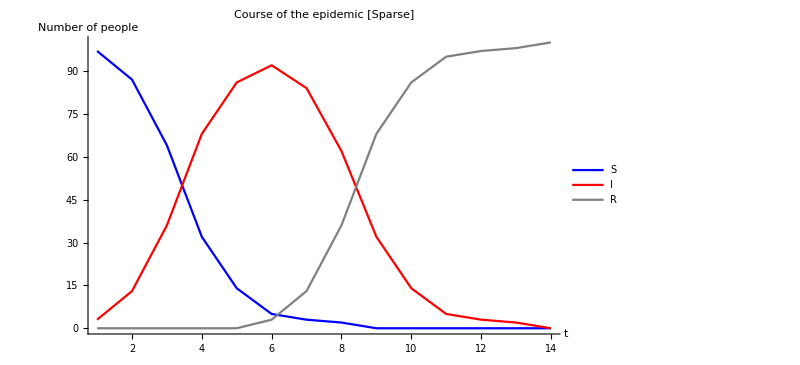

```mathematica
(*Plotting the course of S, I and R*)
plotSSparse = ListLinePlot[listSSparse, PlotStyle->Blue, PlotLegends->{"S"},AxesLabel->{"t", "Number of people"}];
plotISparse = ListLinePlot[listISparse,PlotStyle-> Red, PlotLegends->{"I"}];
plotRSparse = ListLinePlot[listRSparse, PlotStyle-> Gray, PlotLegends->{"R"}];

(*combining the plots from above*)
img = Show[plotSSparse, plotISparse, plotRSparse, PlotRange->All, PlotLabel->"Course of the epidemic [Sparse]"]
```

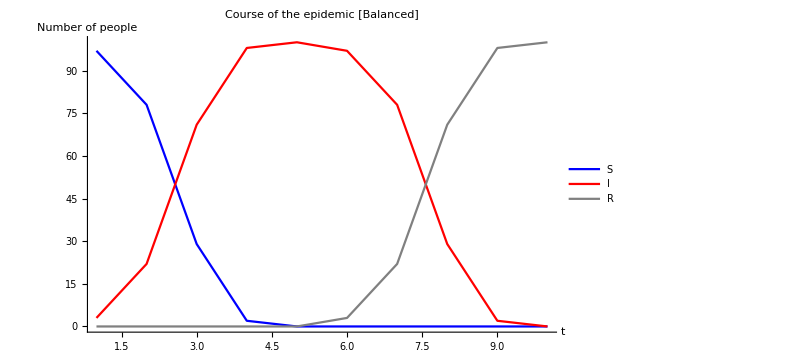

```mathematica
plotSBalanced = ListLinePlot[listSBalanced, PlotStyle->Blue, PlotLegends->{"S"},AxesLabel->{"t", "Number of people"}];
plotIBalanced = ListLinePlot[listIBalanced,PlotStyle-> Red, PlotLegends->{"I"}];
plotRBalanced = ListLinePlot[listRBalanced, PlotStyle-> Gray, PlotLegends->{"R"}];
img = Show[plotSBalanced, plotIBalanced, plotRBalanced, PlotRange->All, PlotLabel->"Course of the epidemic [Balanced]"]
```

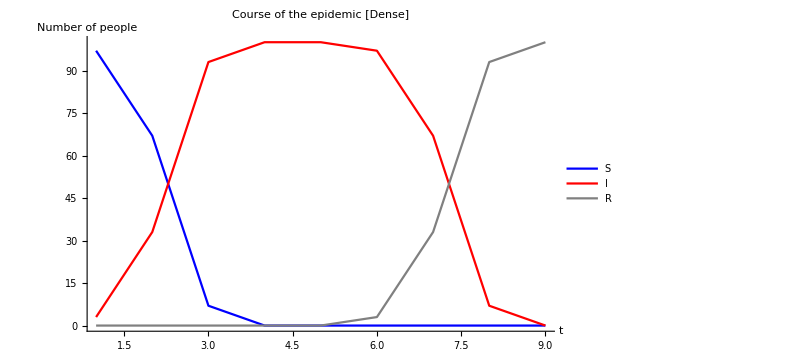

```mathematica
plotSDense = ListLinePlot[listSDense, PlotStyle->Blue, PlotLegends->{"S"}, AxesLabel->{"t", "Number of people"}];
plotIDense = ListLinePlot[listIDense,PlotStyle-> Red, PlotLegends->{"I"}];
plotRDense = ListLinePlot[listRDense, PlotStyle-> Gray, PlotLegends->{"R"}];
img = Show[plotSDense, plotIDense, plotRDense, PlotRange->All, PlotLabel->"Course of the epidemic [Dense]"]
```

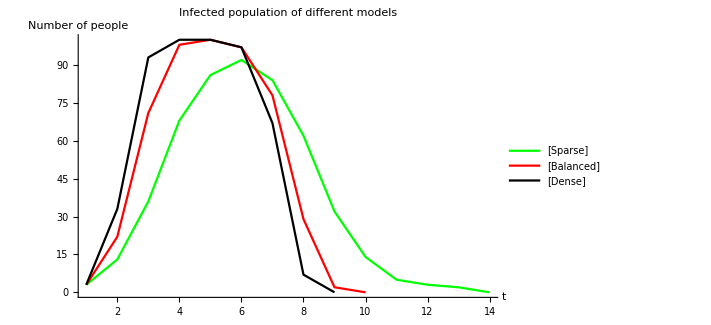

```mathematica
(*Plot only the I- curves for each graph*)
plotISparse = ListLinePlot[listISparse,PlotStyle-> Green, PlotLegends->{"[Sparse]"}, AxesLabel->{"t", "Number of people"}];
plotIBalanced = ListLinePlot[listIBalanced,PlotStyle-> Red, PlotLegends->{"[Balanced]"}];
plotIDense = ListLinePlot[listIDense,PlotStyle-> Black, PlotLegends->{"[Dense]"}];
(*Showing everything together in one plot*)
Show[plotISparse, plotIBalanced, plotIDense, PlotRange->All, PlotLabel->"Infected population of different models"]
```

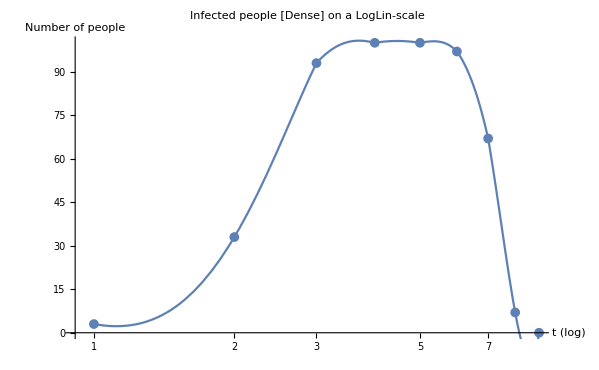

```mathematica
(*interpolating the values to get a nice courve to look at, while the values are plotted on a logarithmic scale*)
f = ListInterpolation[listIDense];

(*Plot the I- values on a LogLin scale to show that the spreading of the epidemic is exponential (hence linear in LogLin)*)
Show[ListLogLinearPlot[listIDense, PlotMarkers->{Automatic, 10}, AxesLabel->{"t (log)", "Number of people"}],


LogLinearPlot[f[x],{x,1,Length[listIDense]}], PlotLabel->"Infected people [Dense] on a LogLin-scale"]
```

```mathematica
Visualizing Wave Sprading Dynamics
```

Dynamics Sprading Visualizing Wave

```mathematica
SeedRandom[42];
n = 1000;
graphCluster = RandomGraph[BarabasiAlbertGraphDistribution[n,1]];
epidemicSimulation[graphCluster, n, 3,5,1.0,30];
(*annotating*)
graphCluster = Annotate[graphCluster, {EdgeStyle->Thin, PlotLabel->"BarabasiAlbertGraphDistribution[1000,1]"}];
(*animating*)
animation = Animate[HighlightGraph[graphCluster,{Style[Flatten[Position[statusListT[[aniStep]],0]],Blue], Style[Flatten[Position[statusListT[[aniStep]],1]],Red], Style[Flatten[Position[statusListT[[aniStep]],2]],Gray]
} ],{aniStep,1,tCurrent+1,1},AnimationRunning->False, AnimationRate->2, AnimationDirection->Forward]

(*Export["/Users/jakob/Desktop/MathematicaProject/wavespreading.mp4",animation];*)
```

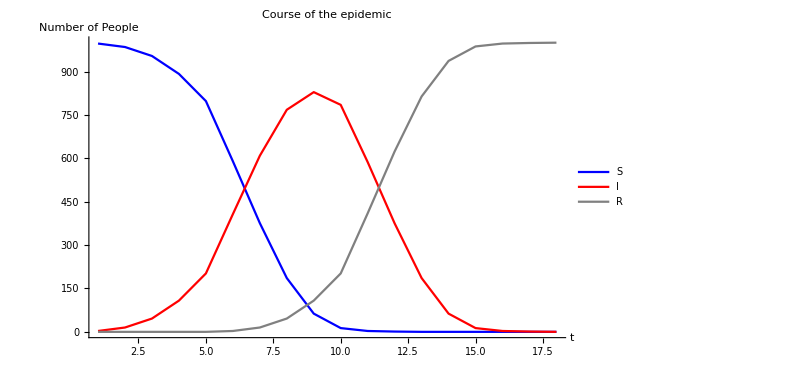

```mathematica
plotS = ListLinePlot[listS, PlotStyle->Blue, PlotLegends->{"S"}, AxesLabel->{"t","Number of People"}];
plotI = ListLinePlot[listI,PlotStyle-> Red,PlotLegends->{"I"}];
plotR = ListLinePlot[listR, PlotStyle-> Gray,PlotLegends->{"R"}];
img = Show[plotS, plotI, plotR, PlotRange->All, PlotLabel-> "Course of the epidemic"]
```

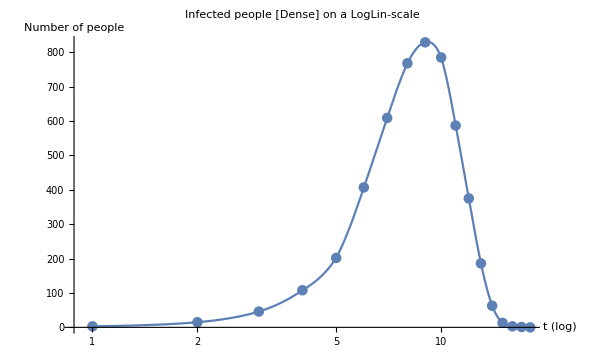

```mathematica
f = ListInterpolation[listI];
Show[ListLogLinearPlot[listI, AxesLabel->{"t (log)", "Number of people"}],LogLinearPlot[f[x],{x,1,Length[listI]}], PlotLabel->"Infected people [Dense] on a LogLin-scale"]
```